# ROM Seminarska Naloga: Sončni sistem

## Zbiranje podatkov:

Podatke o planetih in o njihovih hitrostih sem dobil na http://www.astronomynotes.com/tables/tablesb.htm  in na http://www.ijsrp.org/research-paper-0516/ijsrp-p5328.pdf 

-Graphics--Graphics-

## 2D Oblika:

Na začetku sem ugotovil kako se naredi krog (circle) in nato sem ugotovil kako se naredi iz kroga elipso. Nato sem od vsakega planeta naredil elipso in jo shranil v spremenljivko. Planete sem razvrsil na zunanje in notranje. Vse elipse imajo središče v centru.

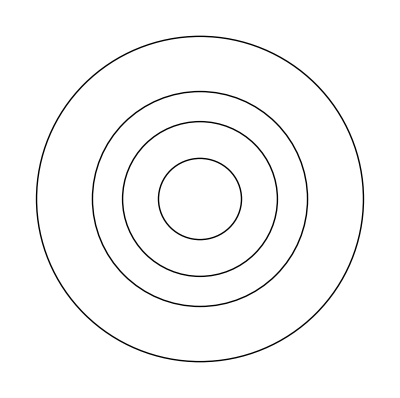
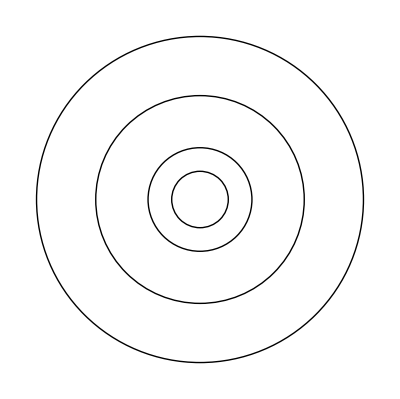

```mathematica
eMerkur =Graphics[Circle[{0,0},{579,566.703}]];
eVenera = Graphics[Circle[{0,0},{1080,1079.974}]];
eZemlja = Graphics[Circle[{0,0},{1500,1499.783}]];
eMars = Graphics[Circle[{0,0},{2280,2269.905}]];
eJupiter =Graphics[Circle[{0,0},{7790,7780.643}]];
eSaturn = Graphics[Circle[{0,0},{14300, 14290}]]; (*48810.149*)
eUran = Graphics[Circle[{0,0},{28700,28669.619}]];
eNeptun = Graphics[Circle[{0,0},{45000,44997.277}]];
eNotranji =Show[eMerkur,eVenera,eZemlja,eMars];
eZunanji = Show[eJupiter,eSaturn,eUran,eNeptun];
{eNotranji,eZunanji}
```

Nato sem vse planete dal v ukaz Graphics in sem jih upodobil kot točke (Points). Dodal sem jim še barvo, velikost in seveda se sonce. Velikost planetov je povečana in so si medseboj enaki in sonce je malo večji, elipse pa so v pravi velikosti.

```mathematica
Graphics[{Gray,PointSize@.03261,Point@{579*Cos[merkur],566.703*Sin[merkur]}},{Red,PointSize@.03,Point@{1080*Cos[venera],1079.974*Sin[venera]}},{Blue,PointSize@.03,Point@{1500*Cos[zemlja],1499.783*Sin[zemlja]}},{Orange,PointSize@.03,Point@{2280*Cos[mars],2269.905*Sin[mars]}},{Yellow,PointSize@0.09298235294,Point[{0,0}]}];
```

Ko sem opravil z velikostjo sem vse podatke spravil v ukaz Animation in izračunal hitrosti s pomočjo Zemlje. Zemljino hitrost sem vstavil pravilno in sem jo pohitril, potem sem pa izračunal vse ostale hitrosti s pomočjo Zemline hitrosti.  Za zunanje planete sem naredil po enakem postopku in sem funkciji spravil v spremenlivki notranjidd in zunanjidd. (Vse hitrosti planetov so pospešene za 10^4 dni.)

```mathematica
notranjidd=Animate[
Graphics[{Circle[{0,0},{579,566.703}],Circle[{0,0},{1080,1079.974}],Circle[{0,0},{1500,1499.783}],Circle[{0,0},{2280,2269.905}],

{Gray,PointSize@.03261,Point@{579*Cos[merkur],566.703*Sin[merkur]}},{Red,PointSize@.03,Point@{1080*Cos[venera],1079.974*Sin[venera]}},{Blue,PointSize@.03,Point@{1500*Cos[zemlja],1499.783*Sin[zemlja]}},{Orange,PointSize@.03,Point@{2280*Cos[mars],2269.905*Sin[mars]}},{Yellow,PointSize@0.09298235294,Point[{0,0}]}}],

{merkur,0,360 Degree,AnimationRate->0.036526*4.15},{venera,0,360 Degree,AnimationRate->0.036526*1.63},{zemlja,0,360 Degree,AnimationRate->0.036526},{mars,0,360 Degree,AnimationRate->0.036526/1.88}];
```

```mathematica
zunanjidd =Animate[
Graphics[{Circle[{0,0},{779,778.0643}],Circle[{0,0},{1430,1429}],Circle[{0,0},{2870,2866.9619}],Circle[{0,0},{4500,4499.7277}],

{Purple,PointSize@.03,Point@{778.3*Cos[jupiter],778.3*Sin[jupiter]}},{Green,PointSize@.03,Point@{1427.0*Cos[saturn],1427.0*Sin[saturn]}},{Blue,PointSize@.03,Point@{2871.0*Cos[uran],2871.0*Sin[uran]}},{Cyan,PointSize@.03,Point@{4497.1*Cos[neptun],4497.1*Sin[neptun]}},{Yellow,PointSize@0.09298235294,Point[{0,0}]}}],

{jupiter,0,360 Degree,AnimationRate->0.036526*.433266667},{saturn,0,360 Degree,AnimationRate->0.036526*.10759346},{uran,0,360 Degree,AnimationRate->0.036526*.0306855218},{neptun,0,360 Degree,AnimationRate->0.036526*0.00601905362}];
```

```mathematica
{notranjidd,zunanjidd}
```

{,}

## 3D Oblika:

Pri 3D obliki sem se lotil zelo podobnega postopka, kot pri 2D ampak pri tem sem moral delati z Graphics3D in pisati različne kordinate, kot naprimer začetna točka in naklone neke elipse. 
Enačba za elipso je: 

-Graphics-,

Da mi je bilo lažje vstavljati podatke sem naredil funkcijo Elipsa3D v katero bom dal spremenljivke planetov. Spremenljivki a in b sta radija elipse , zamik elipse je v spremenljivki P0, n1 in n2 sta kordinate elipse ({x,y,z}), ki sem ju uporabil pri naklonu.

```mathematica
Elipsa3D[a_,b_,P0_,n1_,n2_,Barva_]:=Module[{},ParametricPlot3D[P0+(a Cos[phi]) Normalize[n1]+(b Sin[phi]) Normalize[n2],{phi,-Pi,Pi},Barva]];
```

Pri teh sem naredil podovno kot  pri 2D obliki. Torej sem vse elipso in točke naredil enako velike, naklon sem pa izračunal s pomočjo Pitagorjevega izreka, tako da sem za Zemljo predpostavu, da je Zemlja x os. tako sem preko kota dobil z-e kordinato.

```mathematica
s = Graphics3D[{PointSize[0.1],Yellow, Point[{0,0,0}]}];
p1=Elipsa3D[579,566.703,0,{1000,0,182.9339384},{0,1000,0},PlotStyle->{Gray}];
p2=Elipsa3D[1080,1079.974,0,{1000,0,63.95115639},{0,1000,0},PlotStyle->{Red}];
p3=Elipsa3D[1500,1499.783,0,{1000,0,0},{0,1000,0},PlotStyle->{Blue}];
p4=Elipsa3D[2280,2269.905,0,{1000,0,73.64496949},{0,1000,0},PlotStyle->{Orange}];

p5=Elipsa3D[7790,7780.643,0,{1000,0,17.74139586},{0,1000,0},PlotStyle->{Purple}];
p6=Elipsa3D[14300,14290,0,{1000,0,61.97677025},{0,1000,0},PlotStyle->{Green}];
p7=Elipsa3D[28700,28669.619,0,{1000,0,38.56887014},{0,1000,0},PlotStyle->{Blue}];
p8=Elipsa3D[45000,44997.277,0,{1000,0,138.9148624},{0,1000,0},PlotStyle->{LightBlue}];

dddn =Show[s,p1,p2,p3,p4,PlotRange->All];
dddz =Show[s,p5,p6,p7,p8,PlotRange->All];
dddnz =Show[s,p1,p2,p3,p4,p5,p6,p7,p8,PlotRange->All];
{dddn,dddz,dddnz}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

Nato sem naredil planete, ki so zapisani kot točke (Points) pri njih se nisem ubadal z velikostjo samo s hitrostjo.

```mathematica
Graphics3D[{PointSize[Large],Gray,Point[0+(579*Cos[merkur])*Normalize[{1000,0,182.9339384}]+(566.703*Sin[merkur])*Normalize[{0,1000,0}]]}];Graphics3D[{PointSize[Large],Red,Point[0+(1080*Cos[venera])*Normalize[{1000,0,63.95115639}]+(1079.974*Sin[venera])*Normalize[{0,1000,0}]]}];Graphics3D[{PointSize[Large],Blue,Point[0+(1500*Cos[zemlja])*Normalize[{1000,0,0}]+(1499.783*Sin[zemlja])*Normalize[{0,1000,0}]]}];Graphics3D[{PointSize[Large],Orange,Point[0+(2280*Cos[mars])*Normalize[{1000,0,73.64496949}]+(2269.905*Sin[mars])*Normalize[{0,1000,0}]]}];
```

Vse podatke sem dodalj v ukaz Animation, Show in izračunal hitrosti planetov na enak način kakor pri 2D Obliki. Enako sem naredil pri zunanjih planetih. Obe spremenljivki  sem shranil v notranjiddd in zunanjiddd.

```mathematica
notranjiddd =
Animate[
Show[s,p1,p2,p3,p4,

Graphics3D[{PointSize[Large],Gray,Point[0+(579*Cos[merkur])*Normalize[{1000,0,182.9339384}]+(566.703*Sin[merkur])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],Red,Point[0+(1080*Cos[venera])*Normalize[{1000,0,63.95115639}]+(1079.974*Sin[venera])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],Blue,Point[0+(1500*Cos[zemlja])*Normalize[{1000,0,0}]+(1499.783*Sin[zemlja])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],Orange,Point[0+(2280*Cos[mars])*Normalize[{1000,0,73.64496949}]+(2269.905*Sin[mars])*Normalize[{0,1000,0}]]}]],

{merkur,0,2 Pi,AnimationRate->0.036526*4.15},{venera,0,2 Pi,AnimationRate->0.036526*1.63},{zemlja,0,2 Pi,AnimationRate->0.036526},{mars,0,2 Pi,AnimationRate->0.036526/1.88}];
```

```mathematica
zunanjiddd= 
Animate[
Show[s,p5,p6,p7,p8,

Graphics3D[{PointSize[Large],Purple,Point[0+(7790*Cos[jupiter])*Normalize[{1000,0,17.74139586}]+(7780.643*Sin[jupiter])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],Green,Point[0+(14300*Cos[saturn])*Normalize[{1000,0,61.97677025}]+(4881.149*Sin[saturn])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],Blue,Point[0+(28700*Cos[uran])*Normalize[{1000,0,38.56887014}]+(28669.619*Sin[uran])*Normalize[{0,1000,0}]]}],Graphics3D[{PointSize[Large],LightBlue,Point[0+(45000*Cos[neptun])*Normalize[{1000,0,138.9148624}]+(44997.277*Sin[neptun])*Normalize[{0,1000,0}]]}]],

{jupiter,0,2 Pi,AnimationRate->0.036526*.433266667},{saturn,0,2 Pi,AnimationRate->0.036526*0.00601905362},{uran,0,2 Pi,AnimationRate->0.036526*.0306855218},{neptun,0,2 Pi,AnimationRate->0.036526*0.00601905362}];
```

```mathematica
{notranjiddd,zunanjiddd}
```

{,}